{100,81,64,49,36,25,16,9,4,1}

385

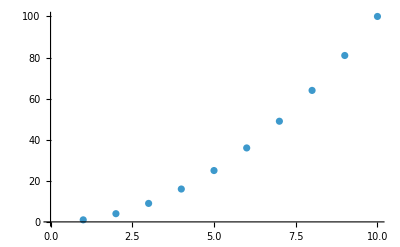

{1,1,2,2,3,3,4,4}

{10,11,12,13,14,15,16,17,18,19,20}

{1,1,4,8,9,16,25,27,64,125}

39

4

{1,2,6,7,6,5,0,6,0,0}

8

28

1

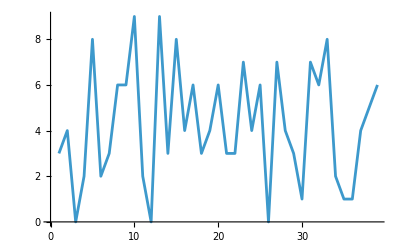

{11,12,13,14,15,16,17,18,19,20}

```mathematica
Reverse[Range[10]^2]
Total[Range[10]^2]
ListPlot[Range[10]^2]
Sort[Join[Range[4],Range[4]]]
Range[11]+9
Sort[Join[Range[5]^2,Range[5]^3]]
Length[IntegerDigits[2^128]]
First[IntegerDigits[2^32]]
Take[IntegerDigits[2^100],10]
Max[IntegerDigits[2^20]]
Count[IntegerDigits[2^1000],0]
Part[Sort[IntegerDigits[2^20]],2]
ListLinePlot[IntegerDigits[2^128]]
Take[Drop[Range[100],10],10]
```

{1000,1000,1000,1000,1000}

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

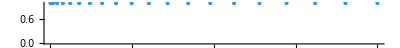

{0,2,4,6,8,10,12,14,16,18,20}

{1,2,3,4,5,6,7,8,9,10}

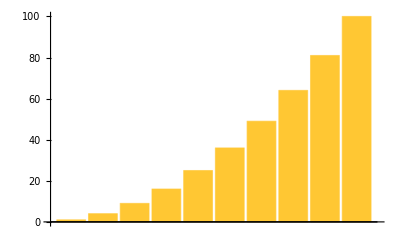

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

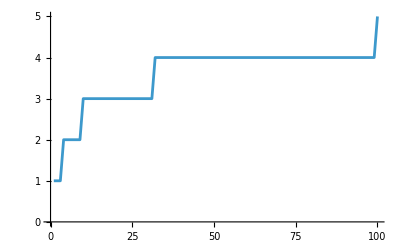

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

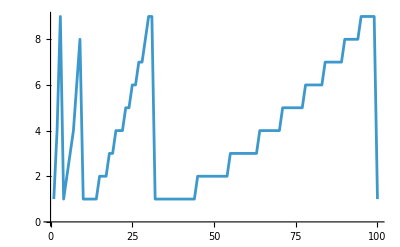

```mathematica
Table[1000,5]
Table[n^3,{n,10,20}]
NumberLinePlot[Range[20]^2]
Table[n,{n,0,20,2}]
Table[n,{n,1,10}]
BarChart[Range[10]^2]
Table[IntegerDigits[n^2],{n,1,10}]
ListLinePlot[Table[Length[IntegerDigits[n^2]],{n,1,100}]]
Table[First[IntegerDigits[n^2]],{n,1,20}]
ListLinePlot[Table[First[IntegerDigits[n^2]],{n,1,100}]]
```

```mathematica
{Red, Yellow, Green}
Column[{Red, Yellow, Green}]
ColorNegate[Orange]
Table[Hue[n],{n,0,1,0.02}]
Table[RGBColor[1,n,1],{n,0,1,0.05}]
Blend[{Pink,Yellow}]
Table[Blend[{Yellow,Hue[n]}],{n,0,1,0.05}]
Table[Style[n,Hue[n]],{n,0,1,0.1}]
Style[Purple,100]
Table[Style[Red,n],{n,10,100,10}]
Style[999,100,Red]
Table[Style[n^2,n^2],{n,0,10}]
Table[Part[{Red,Yellow,Green},RandomInteger[{1,3}]],100]
Table[Style[Part[IntegerDigits[2^1000],n],3*Part[IntegerDigits[2^1000],n]],{n,1,50}]
```

{RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0]}

RGBColor[1, 0, 0]
RGBColor[1, 1, 0]
RGBColor[0, 1, 0]

RGBColor[0., 0.5, 1.]

{Hue[0.],Hue[0.02],Hue[0.04],Hue[0.06],Hue[0.08],Hue[0.1],Hue[0.12],Hue[0.14],Hue[0.16],Hue[0.18],Hue[0.2],Hue[0.22],Hue[0.24],Hue[0.26],Hue[0.28],Hue[0.3],Hue[0.32],Hue[0.34],Hue[0.36],Hue[0.38],Hue[0.4],Hue[0.42],Hue[0.44],Hue[0.46],Hue[0.48],Hue[0.5],Hue[0.52],Hue[0.54],Hue[0.56],Hue[0.58],Hue[0.6],Hue[0.62],Hue[0.64],Hue[0.66],Hue[0.68],Hue[0.7000000000000001],Hue[0.72],Hue[0.74],Hue[0.76],Hue[0.78],Hue[0.8],Hue[0.8200000000000001],Hue[0.84],Hue[0.86],Hue[0.88],Hue[0.9],Hue[0.92],Hue[0.9400000000000001],Hue[0.96],Hue[0.98],Hue[1.]}

{RGBColor[1, 0., 1],RGBColor[1, 0.05, 1],RGBColor[1, 0.1, 1],RGBColor[1, 0.15000000000000002, 1],RGBColor[1, 0.2, 1],RGBColor[1, 0.25, 1],RGBColor[1, 0.30000000000000004, 1],RGBColor[1, 0.35000000000000003, 1],RGBColor[1, 0.4, 1],RGBColor[1, 0.45, 1],RGBColor[1, 0.5, 1],RGBColor[1, 0.55, 1],RGBColor[1, 0.6000000000000001, 1],RGBColor[1, 0.65, 1],RGBColor[1, 0.7000000000000001, 1],RGBColor[1, 0.75, 1],RGBColor[1, 0.8, 1],RGBColor[1, 0.8500000000000001, 1],RGBColor[1, 0.9, 1],RGBColor[1, 0.9500000000000001, 1],RGBColor[1, 1., 1]}

RGBColor[1, 0.75, 0.25]

{RGBColor[1., 0.5, 0.],RGBColor[1., 0.65, 0.],RGBColor[1., 0.8, 0.],RGBColor[1., 0.9500000000000001, 0.],RGBColor[0.8999999999999999, 1., 0.],RGBColor[0.75, 1., 0.],RGBColor[0.5999999999999999, 1., 0.],RGBColor[0.5, 1., 0.050000000000000044],RGBColor[0.5, 1., 0.20000000000000018],RGBColor[0.5, 1., 0.3500000000000001],RGBColor[0.5, 1., 0.5],RGBColor[0.5, 0.8499999999999999, 0.5],RGBColor[0.5, 0.6999999999999997, 0.5],RGBColor[0.5, 0.5499999999999998, 0.5],RGBColor[0.6000000000000001, 0.5, 0.5],RGBColor[0.75, 0.5, 0.5],RGBColor[0.9000000000000004, 0.5, 0.5],RGBColor[1., 0.5, 0.44999999999999973],RGBColor[1., 0.5, 0.2999999999999998],RGBColor[1., 0.5, 0.1499999999999999],RGBColor[1., 0.5, 0.]}

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

RGBColor[0.5, 0, 0.5]

{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}

999

{0,1,4,9,16,25,36,49,64,81,100}

{RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0]}

{1,0,7,1,5,0,8,6,0,7,1,8,6,2,6,7,3,2,0,9,4,8,4,2,5,0,4,9,0,6,0,0,0,1,8,1,0,5,6,1,4,0,4,8,1,1,7,0,5,5}



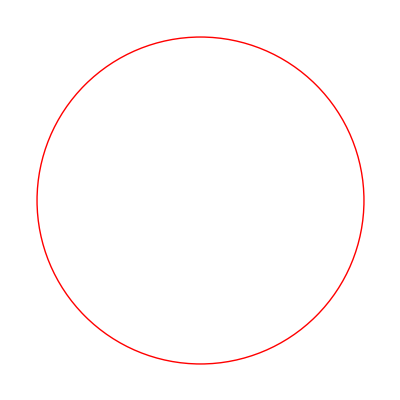

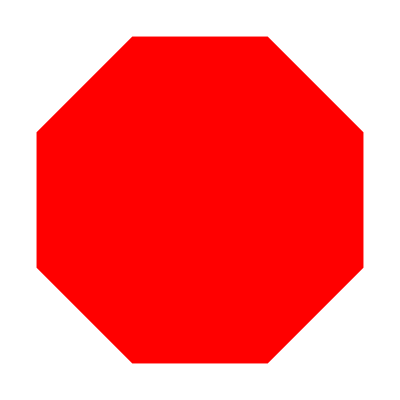


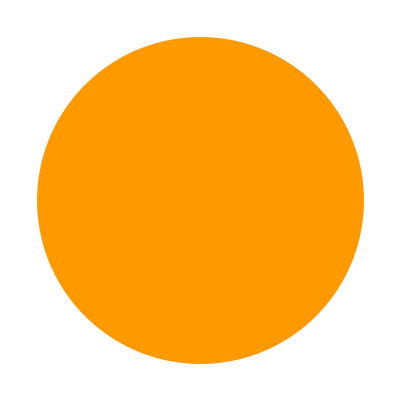
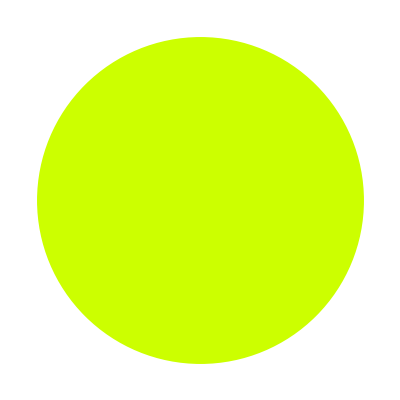
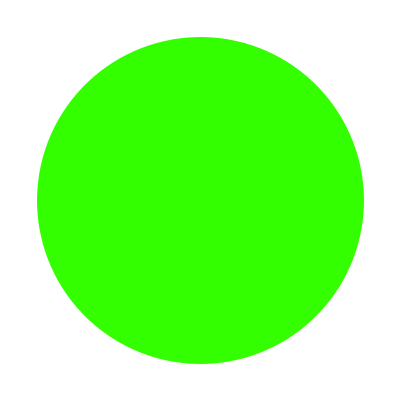
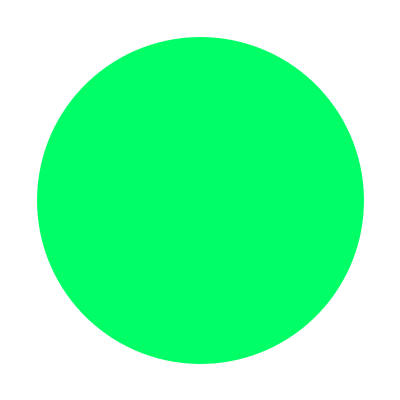
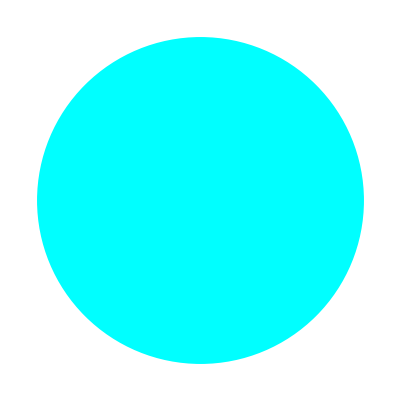
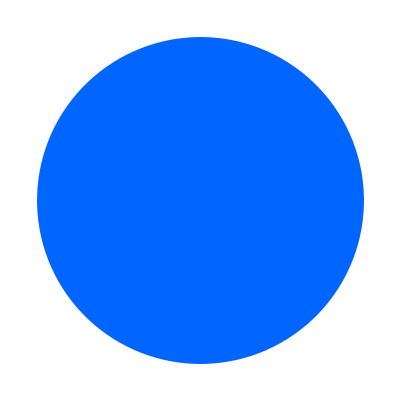
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

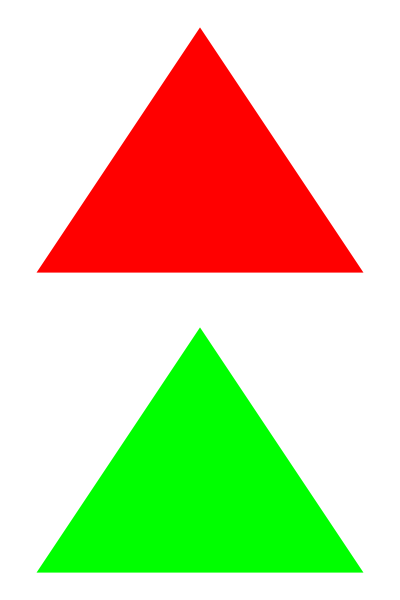

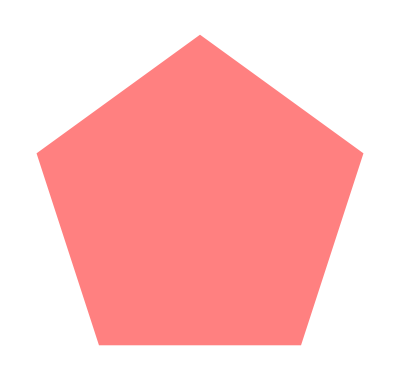
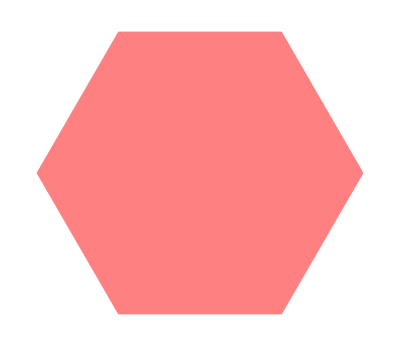
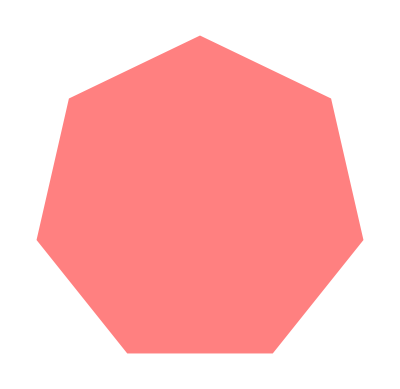
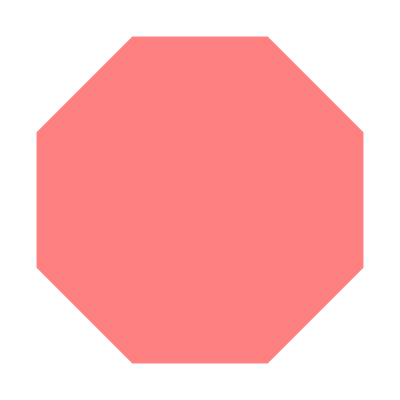
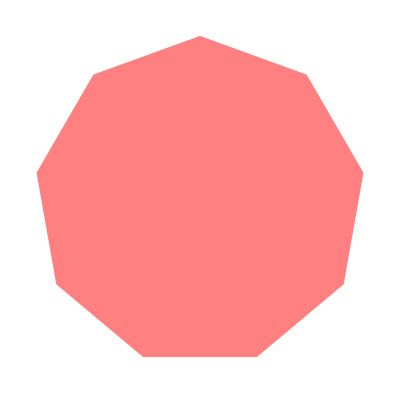
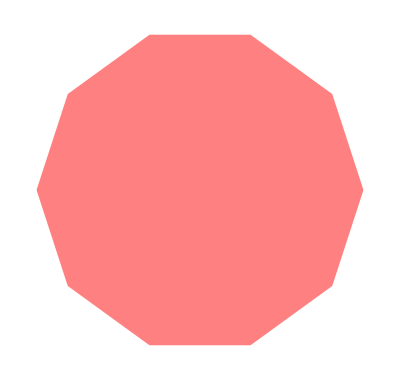

-Graphics3D-

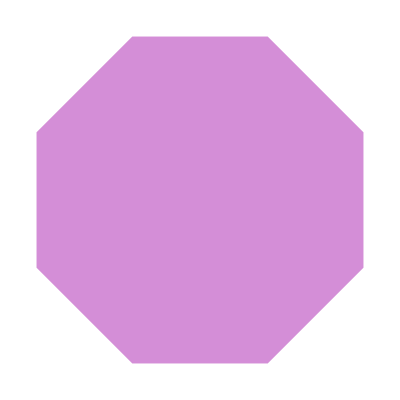
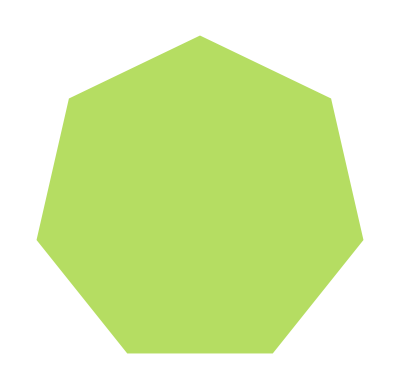
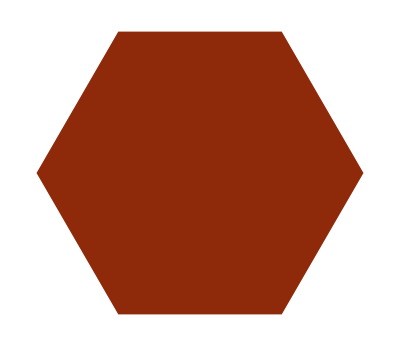
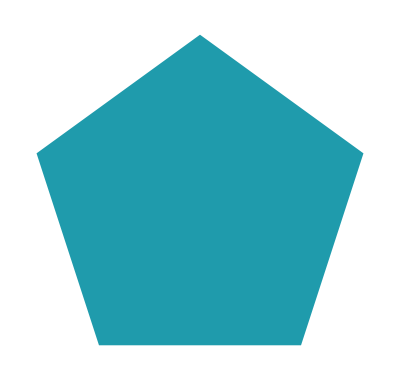
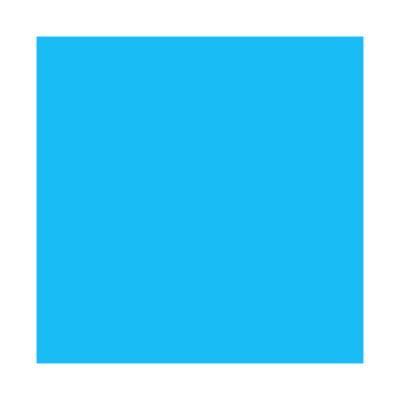
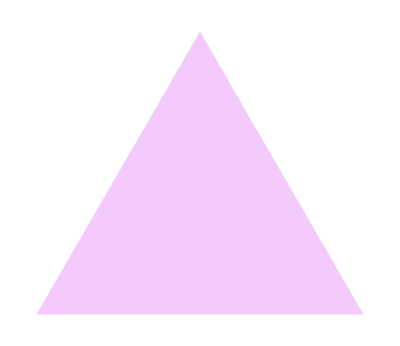

```mathematica
Graphics[RegularPolygon[3]]
Graphics[Style[Circle[],Red]]
Graphics[Style[RegularPolygon[8],Red]]
Table[Graphics[Style[Disk[],Hue[n]]],{n,0,1,0.1}]
Column[{Graphics[Style[RegularPolygon[3],Red]],Graphics[Style[RegularPolygon[3],Green]]}]
Table[Graphics[Style[RegularPolygon[n],Pink]],{n,5,10}]
Graphics3D[Style[Cylinder[],Purple]]
Reverse[Table[Graphics[Style[RegularPolygon[n],RandomColor[]]],{n,3,8}]]
```